```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Lion\Documents\My Projects\GOT\Extract txt

```mathematica
FileNames[]
```

{6pgamesbefore.txt,6pgames.txt,Castles,Castles.nb,Fights,Fights.m,Fights.nb,GetCastles.py,GetFights.py,GetHTML.py,GetNumbersbefore.py,GetNumbers.py,GetOpenings.py,GetWinners.py,htmls,htmls.zip,Numbers,Openings,Openings.m,Openings.nb,ratedgames.txt,RatedvsUnrated.m,RatedvsUnrated.nb,Winners.nb,winners.txt}

```mathematica
winners=Import["winners.txt","Table","FieldSeparators"->","];
winners2=Transpose[winners][[2]];
names={"Lennister","Martell","Tyrell","Graufreud","Stark","Baratheon"};
rate=Table[Count[winners2,names[[i]]],{i,1,Length[names]}];
```

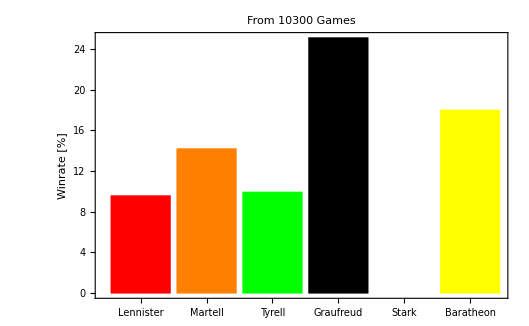

```mathematica
BarChart[rate/Total[rate]*100.,ChartLabels->names,ChartStyle->{Red, Orange, Green, Black,White,Yellow},PlotLabel->StringForm["From `` Games",Length[winners2]],Frame->True,FrameLabel->{None,"Winrate [%]"}]
```

The function that converts a list of positions into the winrate chart:

```mathematica
Find in List
```

```mathematica
MatchQ
```

```mathematica
pos2winners[pos_]:=(
SetDirectory["C:\\Users\\Lion\\Documents\\My Projects\\GOT\\Extract txt"];
winners=Import["winners.txt","Table","FieldSeparators"->","];
winners2=(Transpose[winners][[2]])[[pos]];
names={"Lennister","Martell","Tyrell","Graufreud","Stark","Baratheon"};
rate=Table[Count[winners2,names[[i]]],{i,1,Length[names]}];
BarChart[rate/Total[rate]*100.,ChartLabels->names,ChartStyle->{Red, Orange, Green, Black,White,Yellow},PlotLabel->StringForm["From `` Games",Length[winners2]],Frame->True,FrameLabel->{None,"Winrate [%]"},ImageSize->Large]
)
```

```mathematica
pos2winners[pos_]:=(
SetDirectory["C:\\Users\\Lion\\Documents\\My Projects\\GOT\\Extract txt"];
winners=Import["winners.txt","Table","FieldSeparators"->","];
winners2=(Transpose[winners][[2]])[[pos]];
names={"Lennister","Martell","Tyrell","Graufreud","Stark","Baratheon"};
rate=Table[Count[winners2,names[[i]]],{i,1,Length[names]}];
BarChart[rate/Total[rate]*100.,ChartLabels->names,ChartStyle->{Red, Orange, Green, Black,White,Yellow},PlotLabel->StringForm["From `` Games",Length[winners2]],Frame->True,FrameLabel->{None,"Winrate [%]"},ImageSize->Large]
)
```

```mathematica
rate/Total[rate]*100.
```

{10.5201,17.1395,9.45626,23.1678,24.3499,15.3664}

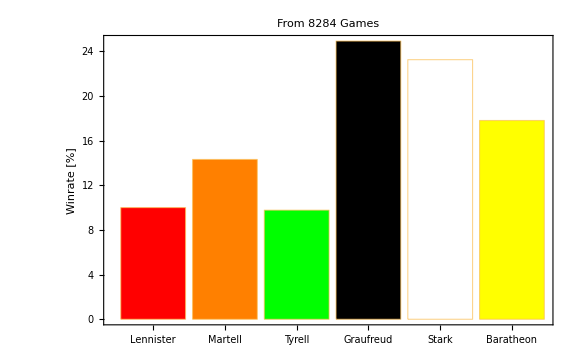
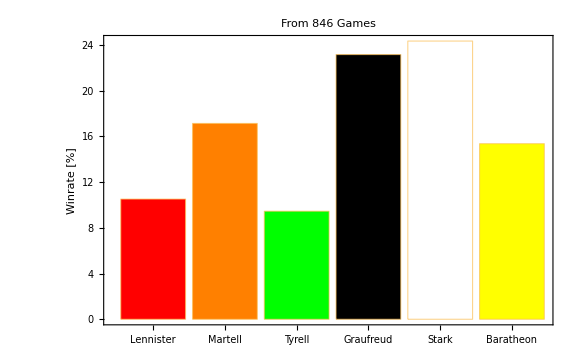

```mathematica
Row[{pos2winners[;;],pos2winners[starkopening]}]
```

```mathematica
(Transpose[winners][[1]])[[positionsGLalliance]]
```

```mathematica
nrs[[positionsGLalliance]]
```